### Introduction

T. Martz-Oberlander 25-10-16
ts.martzoberlander@gmail.com
Mathematica file importer, cleaner, and visualizer for AMOLF solar field data
Please see README.txt file in the home folder for creative commons license 

Organization of code: 
-A Constants and functions repository
-Importing the data where one can choose desired dates
	-pick the directory of your file location, drop extraneous data labels, create absolute time, calculate APE from solar data files
-Creating a master list of module, weather, and APE data* plus calculating observed efficiency
-Selecting data into bins by similar environmental qualities: APE, solar intensity, and air temperature
-Plotting differences in efficiency based on these bins
	-error analysis to ensure comparable efficiency values
Ultimately: Use Tmod, APE, and solar intensity to find comparable obs. eff. time points before comparing clean and dirty data for changes in power output, via efficiency
______________________________

Two main scientific calculations:
Efficiency is calculated: power at max power point (pmpp), which is in the raw data [RD] / panel area * Gpyr solar intensity [also RD]
The APE function: uses integral calculus to find the average energy (eV) of incoming photons from solar intensity [RD]

NB: Run notebook in chronological order as they appear:
functions, imports, munging, comparing, etc. Ideally, just click “Evaluate Notebook”.

NB: Master lists do not contain the entire solar spectra, only pre-calculated APE values. Entire solar spectra lists could be appended to the Masterlists by timestamp by expanding the function in section B.

## Constants Repository Solar Module areas defined here

```mathematica
c = 299792458.; (* units: m / s *)
h = 6.6260695729*10^-34; (* units: J s  - Planck's Constant*)
h2 = 4.136 10^-15(*Planck in eV s*);
q = 1.60217657*10^-19; (* units: Coulombs *)
k = 8.617 * 10^−5; (* units: eV / K *)
T = 300.;(* units: K *)
fac = h c 10^9 /q; (*to convert nm to eV*)
k2= 1.3807 10^-23;(*J/K*)
```

### Area definition

```mathematica
area1 = 2.017*0.494;
area2 = 1.2*0.6;
area3 = 1.675*1.001;
area4 = 1.559*1.046;
area5 = 1.58*0.797;
area6 = 1.656*0.656;
```

0.996398

0.72

1.67668

1.63071

1.25926

1.08634

## Functions Repository All functions stored here for reference

Tutorial: For those new to Mathematica: here is an example function to explain some syntax (here we see the grabber function to pull data based on environmental parameters):

Here is the Mathematica syntax form:
 grabber[list_,APEmin_,APEmax_, Tmin_,Tmax_,Imin_, Imax_]:=Table[{
If[APEmin<list[[i,9,2]]<APEmax&&Tmin<list[[i,2,7]]<Tmax&&Imin<list[[i,3,8]]<Imax,
list[[i]]]},
{i,1,Length[list]}]

And here it is generalized:
For i in list, make a table of data:
	For the ith list in original_dataframe,
		If the 2nd item of the 9th sublist is within the inputted APE range 
		and If the 7th item in the 2nd sublist is within the inputted AirTemp range 
		and If the 8th item in the 3rd sublist is within the inputted solar intensity range
		# and...  Can add other environmental parameters here as desired #
	Put ith list in output_dataframe
Print output_dataframe

### Import functions

For solar spectra and weather data files:

```mathematica
import[directory_,name_]:=Import[directory<>name]; (*eg. NotebookDirectory[],"20161013**.csv"*)
```

### APE function

Function’s required input: a spectra of a given time point from the solar pyranometer datafiles, minimum wavelength, maximum wavelength (eg. 350nm to 1050, since lower and higher wavelength radiation is insignificant for the solar cells); “wl” is the file running through all wavelengths from the min to the max you input; i is the value of incoming radiation in watts/m2/um --> what is UM??

```mathematica
APE[input_,start_,end_] := Quiet[
spectra1 = Interpolation[input];
spectra2 =Interpolation[Table[{i,spectra1[i]*i},{i,input[[1,1]],input[[-1,1]]}]];
NIntegrate[spectra1[wl],{wl,start,end}]/NIntegrate[spectra2[wl] ,{wl,start,end}]]*fac
```

### To Calculate Observed efficiency

ObsEff pulls data from module data files and calculates efficiency from the actual solar panel output.

```mathematica
ObsEff [Pmpp_,Area_, Gpyranometer_] :=100*Pmpp /(Area* Gpyranometer) 
(*ObsEff [list_, Pmpp_,Area_, Gpyranometer_] := Append[list,100*Pmpp /(Area* Gpyranometer) ]*)
```

Meaneff function calculates mean efficiency per module from a MasterList or a more selected list (such as in a bin)

```mathematica
Meaneff[list_,module_]:=Mean[list[[All,module,15]]]
```

### Plot functions

Call the ErrorBarPlots package

```mathematica
Needs["ErrorBarPlots`"]
```

This plots the observed efficiency (from Gpyr and Pmpp) for two groups; clean and dirty

```mathematica
plotobseff[day1_,day2_, module_]:=Table[{DateListPlot[{day1, day2},AxesLabel->{ "Time","% Efficiency"},Frame-> False, PlotLabel-> module"13-10-16 vs. 14-10-16",PlotLegends->{"Dirty (13th)","Clean (14th)"}]},1]
```

This plots module Temperature for two days on one module (eg. plotTmod[module1oct13, module1oct14, 1, “Tmod”])

```mathematica
plotTmod[day1_,day2_, module_,ylabel_]:=Table[{DateListPlot[{day1, day2},AxesLabel->{ "Time",ylabel},Frame-> False, PlotLabel-> module"13-10-16 vs. 14-10-16",PlotLegends->{"13th","14th"}]},1]
```

```mathematica
SpectraPlot[file_,hr_]:=ListPlot[Table[{file[[hr,wl,1]], file[[hr,wl,13]]},{wl,9,2056}],Joined->True]
```

Binplot plots all Efficiency values for each variable bin (Int. APE, Temp) for modules individually

```mathematica
binplot[clean_,dirty_,xaxis_,xlabel_,label_]:=ListPlot[{Transpose[{xaxis,dirty}],Transpose[{xaxis,clean}]},PlotMarkers->Automatic,AxesLabel->{HoldForm[xlabel],HoldForm["% Efficiency"]},PlotLabel->label]
```

Bigplot plots the mean and standard deviation of obs eff from modules in different time stamps by similar environmental variables

```mathematica
bigplot[file1_,file2_]:=Show[
ErrorListPlot[Table[{Mean[file1[[All,i,15]]],StandardDeviation[file1[[All,i,15]]]},{i,3,8}],PlotRange-> {{0,6.2},{0,25}},PlotStyle->Orange, PlotLegends->{"Dirty"}],ErrorListPlot[Table[{Mean[file2[[All,i,15]]],StandardDeviation[file2[[All,i,15]]]},{i,3,8}],PlotStyle->Green, PlotLegends->{"Clean"}],PlotLabel->"Mean Observed Efficiency, dirty versus clean, all Modules",LabelStyle->{GrayLevel[0]},PlotLegends->{"Dirty","Clean"},Frame->{True,True,False,False},FrameLabel->{"Module #", "% Efficiency"}, BaseStyle->{FontWeight->"Bold",Font->"Helvetica",FontSize->10}
]
```

Bigplotgen(eral) plots the mean and stdev for a more general form of file, such as individual bins for each module.

```mathematica
bigplotgen[file1_,file2_]:=Show[
ErrorListPlot[{Mean[file1],StandardDeviation[file1]},PlotStyle->Orange],ErrorListPlot[{Mean[file2],StandardDeviation[file2]},PlotStyle->Green],AxesLabel->{HoldForm[ "Module #"],HoldForm["% Efficiency"]},PlotLabel->"Mean Observed Efficiency, dirty versus clean, all Modules",LabelStyle->{GrayLevel[0]},PlotLegends->{"Dirty","Clean"}
]
```

Errorlistplotgen(erator) plots efficiency and error bars for all modules together

```mathematica
errorlistplotgen[filed1_,filed2_,filed3_,filed4_,filed5_,filed6_,filec1_,filec2_,filec3_,filec4_,filec5_,filec6_]:=ErrorListPlot[{
{{Mean[filed1],StandardDeviation[filed1]},{Mean[filed2],StandardDeviation[filed2]},{Mean[filed3],StandardDeviation[filed3]},{Mean[filed4],StandardDeviation[filed4]},{Mean[filed5],StandardDeviation[filed5]},{Mean[filed6],StandardDeviation[filed6]}},
{{Mean[filec1],StandardDeviation[filec1]},{Mean[filec2],StandardDeviation[filec2]},{Mean[filec3],StandardDeviation[filec3]},{Mean[filec4],StandardDeviation[filec4]},{Mean[filec5],StandardDeviation[filec5]},{Mean[filec6],StandardDeviation[filec6]}}
},
PlotLabel->"Mean of Bins for all Modules",AxesLabel->{HoldForm["Solar Module #" ],HoldForm["% Efficiency"]}]
```

The StDev function is used to compare values of efficiency (item 15 in the final lists) from all modules individually. Input is one file that is less selective in terms of environmental variables and one that is more selective and the numbers 3-8, which correspond to modules 1-6, respectively.

```mathematica
StDev[file1_,file2_,module_]:=StandardDeviation[{Mean[file1[[All,module,15]]],Mean[file2[[All,module,15]]]}]
```

## A. Imports, Cleaning, and Absolute Time

Three types of data inputs from three data logging apparatuses: Weather, Solar Spectra, and Module data
Each section imports, cleans, and converts time and date to AbsoluteTime

## A.1 Weather Each Weather file consists of one hour of data collected every 5mins (so 14 rows of data per file) Imports data by date, as an aggregate of hourly files. The dimensions of this Mathematica list is then: 1day=24 sublists each with 14 sub-sub-lists To clean data of its labels, drop 2 elements every 13 elements The files’ column (aka element) order is as follows: UTC time,Act Air Density,Act Wind Direction,Act Wind Measurement Quality,Act Wind Speed km/u,Avg Absolute air pressure,Avg Air Temprature,Avg Dewpoint temperature,Avg Relative humidity,Avg Wind Speed km/u,Precipitation Intensity mm/h,Precipitation Type

```mathematica
(*choose data directory*)
importweather[directory_,name_]:=Import[SetDirectory[directory],name];
```

```mathematica
weather12= importweather["P:\\Engineering\\SolarField\\Talia\\Data\\weather","Weather_2016-10-12_****.csv"];
weather13= importweather["P:\\Engineering\\SolarField\\Talia\\Data\\weather","Weather_2016-10-13_****.csv"]; 
weather14=importweather["P:\\Engineering\\SolarField\\Talia\\Data\\weather","Weather_2016-10-14_****.csv"];
weather15=importweather["P:\\Engineering\\SolarField\\Talia\\Data\\weather","Weather_2016-10-15_****.csv"];
```

Drop the first and second items from each 1hr file, ever 24 items, to have a clean list of an entire day’s

```mathematica
cleanweather[file_]:=Flatten[Table[Drop[file[[i]], {1,2}], {i, 1,24}] ,1]
```

```mathematica
weathertable12=cleanweather[weather12];
weathertable13=cleanweather[weather13];
weathertable14=cleanweather[weather14];
weathertable15=cleanweather[weather15];
```

This function uses a known date and the 1st item in each weather** file to make an AbsoluteTime stamp. You must list all columns you want listed in this Table.

```mathematica
abstweather[file_,date_]:=Table[{AbsoluteTime[date<>" "<>file[[i,1]]],file[[i,2]],file[[i,3]],file[[i,4]],file[[i,5]],file[[i,6]],file[[i,7]],file[[i,8]],file[[i,9]],file[[i,10]],file[[i,11]],file[[i,12]]},{i,1,Length[file]}]
```

```mathematica
abstweather12=abstweather[weathertable12,"2016.10.12"];
abstweather13=abstweather[weathertable13,"2016.10.13"];
abstweather14=abstweather[weathertable14,"2016.10.14"];
abstweather15=abstweather[weathertable15,"2016.10.15"];
```

All days put into dirty or clean lists

```mathematica
abstweatherdirty=Flatten[Append[{abstweather12},abstweather13],1];
abstweatherclean=Flatten[Append[{abstweather14},abstweather15],1];
```

## A.2 Solar Spectra Data is imported by day, as a list of hourly datafiles Within each spectra there are 24 lists with 2056 items in each list Data columns: Wavelength, Intensity (one value for each 5min time stamp)

```mathematica
SetDirectory["P:\\Engineering\\SolarField\\Talia\\Data\\Spectro\\2016\\"];
```

```mathematica
spectra12=Import["20161012**.csv"];
spectra13 = Import["20161013**.csv"];
spectra14 =Import["20161014**.csv"];
spectra15=Import["20161015**.csv"];
```

### A.2.1 APE Where efficiency increases with increase in photon energy List 8 in Spectra files are the timestamps

Spectra function makes: A table that runs through hour (entire .csv file), which is the 2nd item of the first list of the spectra** import; runs through minute j (columns), which is the 2nd list in the spectra** imports from j=2..13; and makes a list of spectra by hour with each time stamp matched with a wavelength. It runs through all lists of hr h, from the 9th to 2056th item (excluding the labels that come with the data) and from 1-jth minute time stamp within each hr.

```mathematica
Spectra[spectraday_]:=Table[{spectraday[[h,1,2]],spectraday[[h,2,j]],spectraday[[h]][[9;;2056,{1,j}]]},{h,1,24},{j,2,13}]
```

```mathematica
Spectra12=Spectra[spectra12];
Spectra13=Spectra[spectra13];
Spectra14=Spectra[spectra14];
Spectra15=Spectra[spectra15];
```

The SpectraAPE2 function includes date, time, and APE values.

```mathematica
SpectraAPE2[list_]:=Table[{list[[i,j,1]],list[[i,j,2]],APE[list[[i,j, 3]],300,1050]},{i,1,24},{j,1,12}]
```

#### A.2.2 Absolute Time Conversion

Length[flattened_spectradate] is 288=12*24

```mathematica
abstsolar[file_]:=Table[{AbsoluteTime[file[[i,1]]<> " "<>file[[i,2]]],file[[i,3]]},{i,1,Length[file]}]
```

I call the two previous functions at the same time, flattening to reduce the dimensions of sublists

```mathematica
abstAPE12=abstsolar[Flatten[SpectraAPE2[Spectra12],1]];
abstAPE13=abstsolar[Flatten[SpectraAPE2[Spectra13],1]];
abstAPE14=abstsolar[Flatten[SpectraAPE2[Spectra14],1]];
abstAPE15=abstsolar[Flatten[SpectraAPE2[Spectra15],1]];
```

Here I have an appended list of all APE data dates when modules are clean and dirty separately, to be put into a clean and dirty Master list.

```mathematica
abstAPEdirty=Flatten[Append[{abstAPE12},abstAPE13],1];
abstAPEclean=Flatten[Append[{abstAPE14},abstAPE15],1];
```

## A.3 Module Parameters Data is imported by module per month where each file contains a row of data for every 5mins List/datafile length depends on the strength of solar irradiance at early and late times of the day. NB: Must manually convert parameter_*** files to .csv format before importing The files’ column (aka element) order is as follows:

```mathematica
module1Oct= Import[SetDirectory["P:\\Engineering\\SolarField\\Talia\\Data\\log\\"]<>"\\parameter_station1_201610_Module 1.csv", "Table", "NumberPoint"-> ","] ;
module2Oct= Import[SetDirectory["P:\\Engineering\\SolarField\\Talia\\Data\\log\\"]<>"\\parameter_station2_201610_Module 2.csv","Table", "NumberPoint"-> ","];
module3Oct= Import[SetDirectory["P:\\Engineering\\SolarField\\Talia\\Data\\log\\"]<>"\\parameter_station3_201610_Module 3.csv","Table", "NumberPoint"-> ","];
module4Oct= Import[SetDirectory["P:\\Engineering\\SolarField\\Talia\\Data\\log\\"]<>"\\parameter_station4_201610_Module 4.csv","Table", "NumberPoint"-> ","];
module5Oct= Import[SetDirectory["P:\\Engineering\\SolarField\\Talia\\Data\\log\\"]<>"\\parameter_station5_201610_Module 5.csv","Table", "NumberPoint"-> ","];
module6Oct= Import[SetDirectory["P:\\Engineering\\SolarField\\Talia\\Data\\log\\"]<>"\\parameter_station6_201610_Module 6.csv","Table", "NumberPoint"-> ","];
```

#### A.3.2 Absolute Time Conversion

This function uses the 2nd and 3rd items in each module#date file to make an AbsoluteTime stamp and lists other parameters starting with the module m
--Rearranges columns so the module number comes after timestamp
--Rounds the timestamps for the 6 modules to the nearest 100 so that the 5 minute intervals can be matched (instead of having different seconds). Each module timestamp falls within one minute of each other due to sequenced data collection on the solar field computer.

ObsEff is calculated from the 6th and 10th lists’ elements (Pmpp and G_pyr respectively)
In the cleaned Absolute Time modules, ObsEff values are the last and 16th element in each list.

```mathematica
abstmodule[file_,area_]:=Table[{Round[AbsoluteTime[file[[i,2]]<> " "<>file[[i,3]]],100],file[[i,1]],file[[i,4]],file[[i,5]],file[[i,6]],file[[i,7]],file[[i,8]],file[[i,9]],file[[i,10]],file[[i,11]],file[[i,12]],file[[i,13]],file[[i,14]],file[[i,15]],ObsEff[file[[i,6]],area,file[[i,10]]]},{i,1,Length[file]}]
```

### Pulled out data by day, create length values

This creates a list of each panel type based on date; here multiple date files of module data are appended together to create Dirty and Clean lists

Select is used to pick out the dates from the month-long list,
Append creates a long list of dates appended one after the other
Flatten reduces one layer of list depth

```mathematica
module1dirty=abstmodule[Flatten[Append[{Select[module1Oct, MemberQ[#,"12.10.2016"]&]},Select[module1Oct, MemberQ[#,"13.10.2016"]&]],1],area1];
module2dirty=abstmodule[Flatten[Append[{Select[module2Oct, MemberQ[#,"12.10.2016"]&]},Select[module2Oct, MemberQ[#,"13.10.2016"]&]],1],area2];
module3dirty=abstmodule[Flatten[Append[{Select[module3Oct, MemberQ[#,"12.10.2016"]&]},Select[module3Oct, MemberQ[#,"13.10.2016"]&]],1],area3];
module4dirty=abstmodule[Flatten[Append[{Select[module4Oct, MemberQ[#,"12.10.2016"]&]},Select[module4Oct, MemberQ[#,"13.10.2016"]&]],1],area4];
module5dirty=abstmodule[Flatten[Append[{Select[module5Oct, MemberQ[#,"12.10.2016"]&]},Select[module5Oct, MemberQ[#,"13.10.2016"]&]],1],area5];
module6dirty=abstmodule[Flatten[Append[{Select[module6Oct, MemberQ[#,"12.10.2016"]&]},Select[module6Oct, MemberQ[#,"13.10.2016"]&]],1],area6];
```

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:15:00 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:20:00 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:25:00 as a date is ambiguous.

General::stop: Further output of AbsoluteTime::ambig will be suppressed during this calculation.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:15:06 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:20:06 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:25:06 as a date is ambiguous.

General::stop: Further output of AbsoluteTime::ambig will be suppressed during this calculation.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:15:29 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:20:29 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:25:29 as a date is ambiguous.

General::stop: Further output of AbsoluteTime::ambig will be suppressed during this calculation.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:15:37 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:20:37 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:25:37 as a date is ambiguous.

General::stop: Further output of AbsoluteTime::ambig will be suppressed during this calculation.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:15:44 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:20:44 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:25:44 as a date is ambiguous.

General::stop: Further output of AbsoluteTime::ambig will be suppressed during this calculation.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:15:52 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:20:52 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 12.10.2016 10:25:52 as a date is ambiguous.

General::stop: Further output of AbsoluteTime::ambig will be suppressed during this calculation.

```mathematica
module1clean=abstmodule[Flatten[Append[{Select[module1Oct, MemberQ[#,"14.10.2016"]&]},Select[module1Oct, MemberQ[#,"15.10.2016"]&]],1],area1];
module2clean=abstmodule[Flatten[Append[{Select[module2Oct, MemberQ[#,"14.10.2016"]&]},Select[module2Oct, MemberQ[#,"15.10.2016"]&]],1],area2];
module3clean=abstmodule[Flatten[Append[{Select[module3Oct, MemberQ[#,"14.10.2016"]&]},Select[module3Oct, MemberQ[#,"15.10.2016"]&]],1],area3];
module4clean=abstmodule[Flatten[Append[{Select[module4Oct, MemberQ[#,"14.10.2016"]&]},Select[module4Oct, MemberQ[#,"15.10.2016"]&]],1],area4];
module5clean=abstmodule[Flatten[Append[{Select[module5Oct, MemberQ[#,"14.10.2016"]&]},Select[module5Oct, MemberQ[#,"15.10.2016"]&]],1],area5];
module6clean=abstmodule[Flatten[Append[{Select[module6Oct, MemberQ[#,"14.10.2016"]&]},Select[module6Oct, MemberQ[#,"15.10.2016"]&]],1],area6];
```

## B. Creating master lists

This section creates a master list by grouping the three data types--solar, weather, and 6 module files-- by their absolute time stamps into one main list of lists. The selValue function selects data at a certain level in the original list; then a function loops through all inputted data in the selValue to match time (element [[1]]) into the empty newList__.

Entire list is 288 lists long, for the 288 5 minute time stamps per each 24hrs.
Since Module data does not log for 24 hrs, there will be “none” values before ~9.30 and after ~17.30

SelValue inputs: the data file/list name and the level in the list in which the timestamp is found (eg. the first element [[1]])

NewList** is a list of 9 lists as follows:
-newList**[[i,1]]: time stamp
-newList**[[i,2]]: weather file
-newList**[[i,3;;8]]: module files
-newList**[[i,9]]: APE values

```mathematica
selValue[data_,level_]:=If[data=={},{"None"},data[[level]]]
```

```mathematica
timelistclean=abstweatherclean[[All,1]];
```

```mathematica
masterlistclean={};
For[i=1,i<Length[timelistclean]+1,i++,
AppendTo[masterlistclean,DeleteCases[
Join[{timelistclean[[i]]},
selValue[Select[abstweatherclean,#[[1]]==timelistclean[[i]]&],All],
selValue[Select[module1clean,#[[1]]==timelistclean[[i]]&],All],
selValue[Select[module2clean,#[[1]]==timelistclean[[i]]&],All],
selValue[Select[module3clean,#[[1]]==timelistclean[[i]]&],All],
selValue[Select[module4clean,#[[1]]==timelistclean[[i]]&],All],
selValue[Select[module5clean,#[[1]]==timelistclean[[i]]&],All],
selValue[Select[module6clean,#[[1]]==timelistclean[[i]]&],All],
selValue[Select[abstAPEclean,#[[1]]==timelistclean[[i]]&],All]]
,"None",1]]]
```

```mathematica
timelistdirty=abstweatherdirty[[All,1]];
```

```mathematica
masterlistdirty={};
For[i=1,i<Length[timelistdirty]+1,i++,
AppendTo[masterlistdirty,DeleteCases[
Join[{timelistdirty[[i]]},
selValue[Select[abstweatherdirty,#[[1]]==timelistdirty[[i]]&],All],
selValue[Select[module1dirty,#[[1]]==timelistdirty[[i]]&],All],
selValue[Select[module2dirty,#[[1]]==timelistdirty[[i]]&],All],
selValue[Select[module3dirty,#[[1]]==timelistdirty[[i]]&],All],
selValue[Select[module4dirty,#[[1]]==timelistdirty[[i]]&],All],
selValue[Select[module5dirty,#[[1]]==timelistdirty[[i]]&],All],
selValue[Select[module6dirty,#[[1]]==timelistdirty[[i]]&],All],
selValue[Select[abstAPEdirty,#[[1]]==timelistdirty[[i]]&],All]]
,"None",1]]]
```

Now we have a dirty and a clean master list with: 
1st elements: time stamp,
2nd: weather data (sub-elements)
3rd-8th: module data 1 through 6 (each with sub-elements)
9th: APE value

Using Cases allows us to keep only time stamps which have all 6 modules data

```mathematica
mldfinal=Cases[masterlistdirty,{_,_,_,_,_,_,_,_,_}];
mlcfinal=Cases[masterlistclean,{_,_,_,_,_,_,_,_,_}];
```

## C. Grabber Function, to make lists based on input variable conditions

Searches through clean and dirty dat separately to find comparable data by environmental variable
Makes a list from masterlist to smaller bins that satisfy inputs

Inputs currently: min/max of Tair, Intensity, and APE ranges
How to generalize: edit the function within the “If” clause to have more or less or different && requirements.

NB: takes Intensity G_pyr from module1 files only (sampled on the 5 minute mark), as opposed to G_pyr values for each module which can take up to 30sec from initial Module1 measurement

How to know where in the masterlists to search:
In MasterList[dirty]/[clean]:
-Tair is the [[i,2,7]] in weather files
-APE is the [[i,9,2]] in solar files
-I is the [[i,3,8]] in module1 lists (it was 10th item but then I added absolute time in front)

```mathematica
grabber[list_,APEmin_,APEmax_, Tmin_,Tmax_,Imin_, Imax_]:=Table[{
If[APEmin<list[[i,9,2]]<APEmax&&Tmin<list[[i,2,7]]<Tmax&&Imin<list[[i,3,8]]<Imax,
list[[i]]]},
{i,1,Length[list]}]
```

## D. Generating these data bins Each title shows the range of the variable and number of items in clean and dirty bins {dirty,clean}

### APE.BIN 1I - 1.86-1.9 ; {7, 36}

```mathematica
bin2dirty=DeleteCases[Flatten[grabber[mldfinal,1.86,1.9,5,25,0,1000],1],Null,3];
bin2clean=DeleteCases[Flatten[grabber[mlcfinal,1.86,1.9,5,25,0,1000],1],Null,3];
```

```mathematica
Length[bin2dirty]
Length[bin2clean]
```

7

36

### APE.BIN III - 1.90-1.94 ; {52, 43}

```mathematica
bin3dirty=DeleteCases[Flatten[grabber[mldfinal,1.9,1.94,5,25,0,1000],1],Null,3];
bin3clean=DeleteCases[Flatten[grabber[mlcfinal,1.9,1.94,5,25,0,1000],1],Null,3];
```

```mathematica
Length[bin3dirty]
Length[bin3clean]
```

52

43

### APE.BIN IV - 1.94-1.98; {3,5}

```mathematica
bin4dirty=DeleteCases[Flatten[grabber[mldfinal,1.94,1.98,5,25,0,1000],1],Null,3];
bin4clean=DeleteCases[Flatten[grabber[mlcfinal,1.94,1.98,5,25,0,1000],1],Null,3];
```

```mathematica
Length[bin4dirty]
Length[bin4clean]
```

3

5

#### APE Plot, Bins II-IV

```mathematica
ape1={{1.88,Meanobseff[bin2dirty,3]},{1.88,Meanobseff[bin2clean,3]}}
ape2={{1.92,Meanobseff[bin3dirty,3]},{1.92,Meanobseff[bin3clean,3]}}
ape3={{1.96,Meanobseff[bin4dirty,3]},{1.96,Meanobseff[bin3clean,3]}}
```

{{1.88,Meanobseff[{{3685362300,{3685362300,1.23796,55.1643,100,3.6779,1015.13,11.488,6.59967,71.939,6.52281,0,No precipitation},5,{3685362300,6,73.102,0.3864,28.246,85.674,0.4482,73.6,225.7,13.6,233.3,2,0,300,11.5202},{3685362300,1.89112}},5,{1}},3]},{1.88,1}}
 |  |  |  |

{{1.92,Meanobseff[{{3685341900,{3685341900,1.24865,13.7972,100,9.16662,1018.54,10.0127,5.52039,73.6568,7.17955,0,No precipitation},5,{3685341900,6,68.227,0.1553,10.595,82.225,0.1855,69.5,101.9,10.4,104.1,2,0,200,9.57112},{3685341900,1.9094}},50,{1}},3]},{1.92,1}}
 |  |  |  |

{{1.96,Meanobseff[{{3685354800,{3685354800,1.2415,14.707,100,7.84736,1016.41,11.0364,5.93819,70.8208,6.91319,0,No precipitation},5,{3685354800,6,69.765,0.1413,9.858,82.257,0.1765,67.9,97.6,11.1,99.3,2,0,100,9.29768},{3685354800,1.94184}},{1},{1}},3]},{1.96,1}}
 |  |  |  |

```mathematica
Show[
ListPlot[ape1,AxesLabel->{HoldForm["Bin #" ],HoldForm[% Efficiency]},PlotStyle->Blue,PlotRange->{{1.8,2.1},{5,10}}],ListPlot[ape2,PlotStyle->Green],ListPlot[ape3,PlotStyle->Orange]
]
```

-Graphics-

### Intensity BIN V; 63-67 W/m2; {45,81}

```mathematica
bin5dirty=DeleteCases[Flatten[grabber[mldfinal,0,3,5,25,63,67],1],Null,3];
bin5clean=DeleteCases[Flatten[grabber[mlcfinal,0,3,5,25,63,67],1],Null,3];
```

```mathematica
Length[bin5dirty]
Length[bin5clean]
```

45

81

### Intensity BIN VI; 58-63 W/m2; {45,11}

```mathematica
bin6dirty=DeleteCases[Flatten[grabber[mldfinal,0,3,5,25,58,63],1],Null,3];
bin6clean=DeleteCases[Flatten[grabber[mlcfinal,0,3,5,25,58,63],1],Null,3];
```

```mathematica
Length[bin6dirty]
Length[bin6clean]
```

14

11

### Temp BIN VII; 9.5-10.5 C; {5,5}

```mathematica
bin7dirty=DeleteCases[Flatten[grabber[mldfinal,0,3,9.5,10.5,0,100],1],Null,3];
bin7clean=DeleteCases[Flatten[grabber[mlcfinal,0,3,9.5,10.5,0,100],1],Null,3];
```

```mathematica
Length[bin7dirty]
Length[bin7clean]
```

5

5

### Temp BIN VIII; 10.5-11.5 C; {49,14}

```mathematica
bin8dirty=DeleteCases[Flatten[grabber[mldfinal,0,3,10.5,11.5,0,100],1],Null,3];
bin8clean=DeleteCases[Flatten[grabber[mlcfinal,0,3,10.5,11.5,0,100],1],Null,3];
```

```mathematica
Length[bin8dirty]
Length[bin8clean]
```

49

14

### Temp BIN IX; 11.5-12.5 C; {9,14}

```mathematica
bin9dirty=DeleteCases[Flatten[grabber[mldfinal,0,3,11.5,12.5,0,100],1],Null,3];
bin9clean=DeleteCases[Flatten[grabber[mlcfinal,0,3,11.5,12.5,0,100],1],Null,3];
```

```mathematica
Length[bin9dirty]
Length[bin9clean]
```

9

14

## E. Plots: clean-dirty efficiency comparison

### E.1 Bin Comparisons, for each 3 categories (APE, Temp., Int.); examine affects of env. on eff.

The following list contains all plots of efficiency per bin per module (8 bins x 6 modules = 32 plots total)
Also need stdev error bars for y axis and manually input x error from the variables’ range

#### E.1.1 APE

```mathematica
Meaneff[list_,module_]:=Mean[list[[All,module,15]]]
```

List of APE bins per Module:

```mathematica
A1d={Meaneff[bin2dirty,3],Meaneff[bin3dirty,3],Meaneff[bin4dirty,3]};
A1c={Meaneff[bin2clean,3],Meaneff[bin3clean,3],Meaneff[bin4clean,3]};
Ax={1.88,1.92,1.96};
A2d={Meaneff[bin2dirty,3],Meaneff[bin3dirty,3],Meaneff[bin4dirty,3]};
A2c={Meaneff[bin2clean,3],Meaneff[bin3clean,3],Meaneff[bin4clean,3]};
A3d={Meaneff[bin2dirty,3],Meaneff[bin3dirty,3],Meaneff[bin4dirty,3]};
A3c={Meaneff[bin2clean,3],Meaneff[bin3clean,3],Meaneff[bin4clean,3]};
A4d={Meaneff[bin2dirty,3],Meaneff[bin3dirty,3],Meaneff[bin4dirty,3]};
A4c={Meaneff[bin2clean,3],Meaneff[bin3clean,3],Meaneff[bin4clean,3]};
A5d={Meaneff[bin2dirty,3],Meaneff[bin3dirty,3],Meaneff[bin4dirty,3]};
A5c={Meaneff[bin2clean,3],Meaneff[bin3clean,3],Meaneff[bin4clean,3]};
A6d={Meaneff[bin2dirty,3],Meaneff[bin3dirty,3],Meaneff[bin4dirty,3]};
A6c={Meaneff[bin2clean,3],Meaneff[bin3clean,3],Meaneff[bin4clean,3]};
```

List of APE Plots per Module

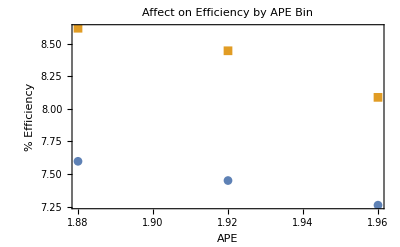

```mathematica
ListPlot[{Transpose[{Ax,A1d}],Transpose[{Ax,A1c}]},PlotMarkers->Automatic,FrameLabel->{"APE","% Efficiency"},PlotLabel->"Affect on Efficiency by APE Bin",Frame->{{True,False},{True,False}},LabelStyle->{FontSize->12,FontFamily->"Helvetica",GrayLevel[0.1]}]
```

Error Plots below needs different colours

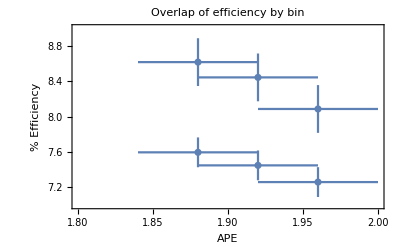

```mathematica
ErrorListPlot[{
{{1.88,Meaneff[bin2dirty,3]},ErrorBar[0.04,StandardDeviation[A1d]]},
,{{1.88,Meaneff[bin2clean,3]},ErrorBar[0.04,StandardDeviation[A1c]]},

{{1.92,Meaneff[bin3dirty,3]},ErrorBar[0.04,StandardDeviation[A1d]]},
,{{1.92,Meaneff[bin3clean,3]},ErrorBar[0.04,StandardDeviation[A1c]]},

{{1.96,Meaneff[bin4dirty,3]},ErrorBar[0.04,StandardDeviation[A1d]]},
,{{1.96,Meaneff[bin4clean,3]},ErrorBar[0.04,StandardDeviation[A1c]]}

},PlotRange->{{1.8,2},{7,9}},PlotLabel->"Overlap of efficiency by bin",Frame->{{True,False},{True,False}},FrameLabel->{"APE","% Efficiency"},LabelStyle->{FontSize->12,FontFamily->"Times New Roman",GrayLevel[0.1]}]
```

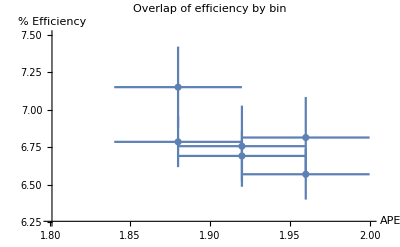

```mathematica
ErrorListPlot[{
{{1.88,Meaneff[bin2dirty,4]},ErrorBar[0.04,StandardDeviation[A1d]]},
,{{1.88,Meaneff[bin2clean,4]},ErrorBar[0.04,StandardDeviation[A1c]]},

{{1.92,Meaneff[bin3dirty,4]},ErrorBar[0.04,StandardDeviation[A1d]]},
,{{1.92,Meaneff[bin3clean,4]},ErrorBar[0.04,StandardDeviation[A1c]]},

{{1.96,Meaneff[bin4dirty,4]},ErrorBar[0.04,StandardDeviation[A1d]]},
,{{1.96,Meaneff[bin4clean,4]},ErrorBar[0.04,StandardDeviation[A1c]]}

},PlotRange->{{1.8,2},{6.25,7.5}},AxesLabel->{HoldForm["APE" ],HoldForm[% Efficiency]}, PlotLabel->"Overlap of efficiency by bin"]
```

etc. for other modules

```mathematica
Needs["ErrorListPlots`"]
```

Get::noopen: Cannot open ErrorListPlots`.

Needs::nocont: Context ErrorListPlots` was not created when Needs was evaluated.

$Failed

#### E.1.2 Temperature

```mathematica
Temp1d={Meaneff[bin7dirty,3],Meaneff[bin8dirty,3],Meaneff[bin9dirty,3]};
Temp1c={Meaneff[bin7clean,3],Meaneff[bin8clean,3],Meaneff[bin9clean,3]};
Tempx={10,11,12};

Temp2d={Meaneff[bin7dirty,4],Meaneff[bin8dirty,4],Meaneff[bin9dirty,4]};
Temp2c={Meaneff[bin7clean,4],Meaneff[bin8clean,4],Meaneff[bin9clean,4]};
Temp3d={Meaneff[bin7dirty,5],Meaneff[bin8dirty,5],Meaneff[bin9dirty,5]};
Temp3c={Meaneff[bin7clean,5],Meaneff[bin8clean,5],Meaneff[bin9clean,5]};
Temp4d={Meaneff[bin7dirty,6],Meaneff[bin8dirty,6],Meaneff[bin9dirty,6]};
Temp4c={Meaneff[bin7clean,6],Meaneff[bin8clean,6],Meaneff[bin9clean,6]};
Temp5d={Meaneff[bin7dirty,7],Meaneff[bin8dirty,7],Meaneff[bin9dirty,7]};
Temp5c={Meaneff[bin7clean,7],Meaneff[bin8clean,7],Meaneff[bin9clean,7]};
Temp6d={Meaneff[bin7dirty,8],Meaneff[bin8dirty,8],Meaneff[bin9dirty,8]};
Temp6c={Meaneff[bin7clean,8],Meaneff[bin8clean,8],Meaneff[bin9clean,8]};
```

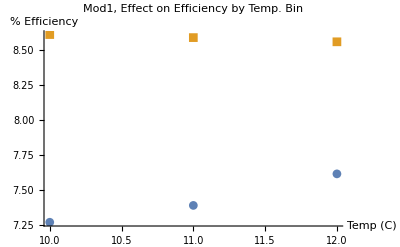

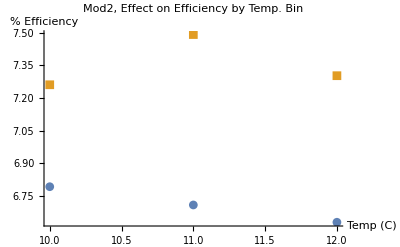

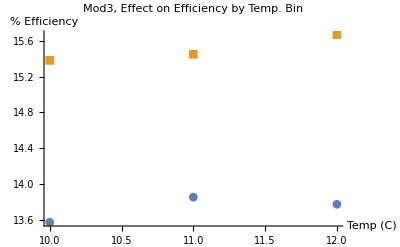

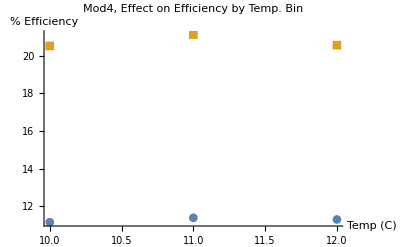

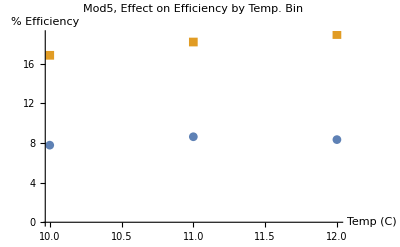

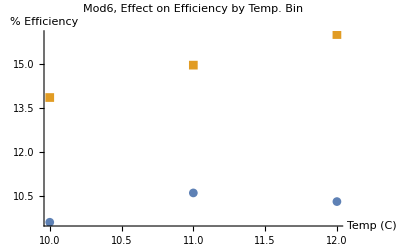

```mathematica
binplot[Temp1c, Temp1d, Tempx, "Temp (C)", "Mod1, Effect on Efficiency by Temp. Bin"]
binplot[Temp2c, Temp2d, Tempx, "Temp (C)", "Mod2, Effect on Efficiency by Temp. Bin"]
binplot[Temp3c, Temp3d, Tempx, "Temp (C)", "Mod3, Effect on Efficiency by Temp. Bin"]
binplot[Temp4c, Temp4d, Tempx, "Temp (C)", "Mod4, Effect on Efficiency by Temp. Bin"]
binplot[Temp5c, Temp5d, Tempx, "Temp (C)", "Mod5, Effect on Efficiency by Temp. Bin"]
binplot[Temp6c, Temp6d, Tempx, "Temp (C)", "Mod6, Effect on Efficiency by Temp. Bin"]
```

#### E.1.3 Solar Intensity

```mathematica
Int1d={Meaneff[bin5dirty,3],Meaneff[bin6dirty,3]};
Int1c={Meaneff[bin5clean,3],Meaneff[bin6clean,3]};
Intx={60.5,65};
```

```mathematica
Int2d={Meaneff[bin5dirty,4],Meaneff[bin6dirty,4]};
Int2c={Meaneff[bin5clean,4],Meaneff[bin6clean,4]};
```

```mathematica
Int3d={Meaneff[bin5dirty,5],Meaneff[bin6dirty,5]};
Int3c={Meaneff[bin5clean,5],Meaneff[bin6clean,5]};
```

```mathematica
Int4d={Meaneff[bin5dirty,6],Meaneff[bin6dirty,6]};
Int4c={Meaneff[bin5clean,6],Meaneff[bin6clean,6]};
```

```mathematica
Int5d={Meaneff[bin5dirty,7],Meaneff[bin6dirty,7]};
Int5c={Meaneff[bin5clean,7],Meaneff[bin6clean,7]};
```

```mathematica
Int6d={Meaneff[bin5dirty,8],Meaneff[bin6dirty,8]};
Int6c={Meaneff[bin5clean,8],Meaneff[bin6clean,8]};
```

Plots

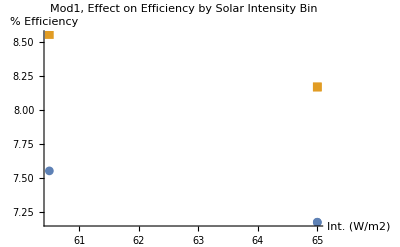

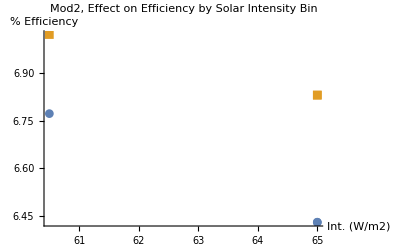

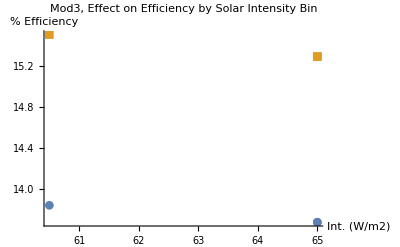

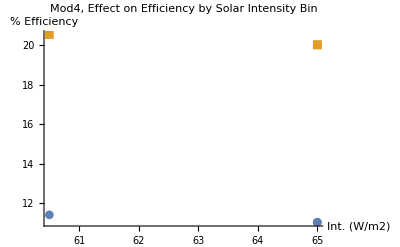

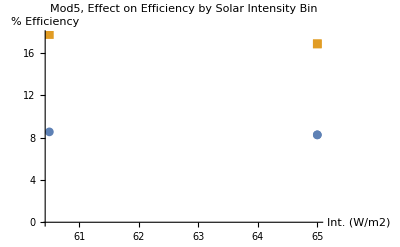

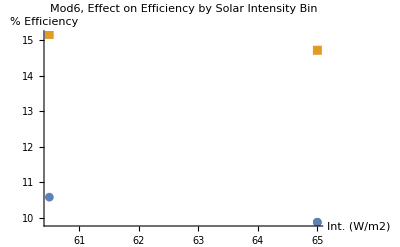

```mathematica
binplot[Int1c, Int1d, Intx, "Int. (W/m2)", "Mod1, Effect on Efficiency by Solar Intensity Bin"]
binplot[Int2c, Int2d, Intx, "Int. (W/m2)", "Mod2, Effect on Efficiency by Solar Intensity Bin"]
binplot[Int3c, Int3d, Intx, "Int. (W/m2)", "Mod3, Effect on Efficiency by Solar Intensity Bin"]
binplot[Int4c, Int4d, Intx, "Int. (W/m2)", "Mod4, Effect on Efficiency by Solar Intensity Bin"]
binplot[Int5c, Int5d, Intx, "Int. (W/m2)", "Mod5, Effect on Efficiency by Solar Intensity Bin"]
binplot[Int6c, Int6d, Intx, "Int. (W/m2)", "Mod6, Effect on Efficiency by Solar Intensity Bin"]
```

### All Bins: 3 APE, 2 Int., 3 Temp.; look for differences in modules for env factors

Uses the bigplot function which plots the mean and standard deviation of obs eff from modules in different time stamps by similar environmental variables

```mathematica
bigplot[file1_,file2_,plotlabel_]:=Show[
ErrorListPlot[Table[{Mean[file1[[All,i,15]]],StandardDeviation[file1[[All,i,15]]]},{i,3,8}],PlotRange-> {{0,6.2},{0,25}},PlotStyle->Orange],
ErrorListPlot[Table[{Mean[file2[[All,i,15]]],StandardDeviation[file2[[All,i,15]]]},{i,3,8}],PlotStyle->Green],
AxesLabel->{HoldForm[ "Module #"],HoldForm["% Efficiency"]},
PlotLabel->plotlabel,
LabelStyle->{GrayLevel[0]},PlotLegends->{"Dirty","Clean"}
]
```

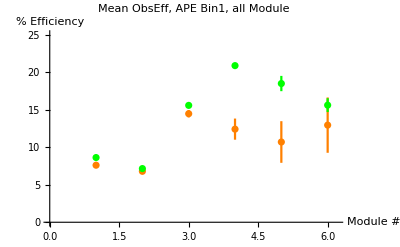

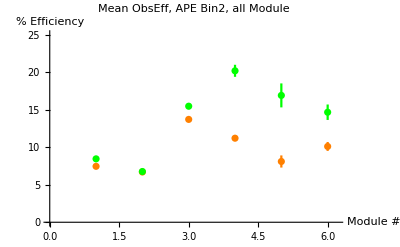

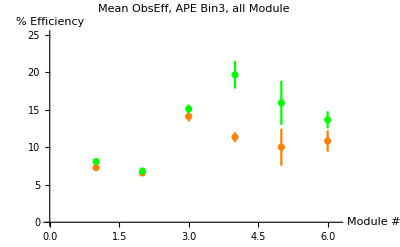

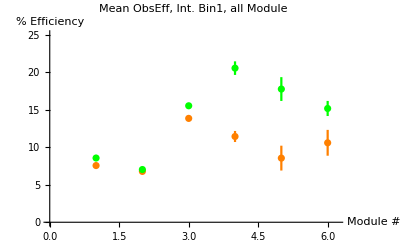

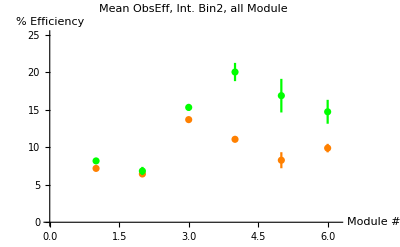

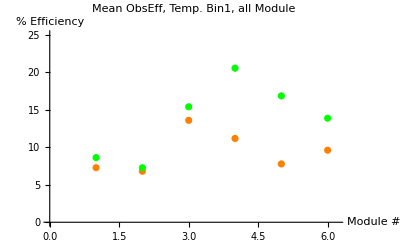

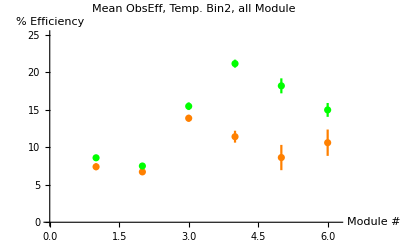

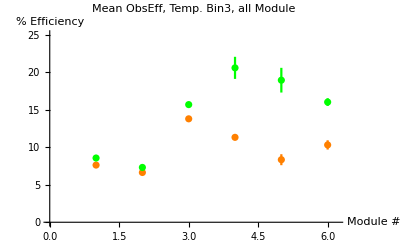

```mathematica
bigplot[bin2dirty,bin2clean,"Mean ObsEff, APE Bin1, all Module"]
bigplot[bin3dirty,bin3clean,"Mean ObsEff, APE Bin2, all Module"]
bigplot[bin4dirty,bin4clean,"Mean ObsEff, APE Bin3, all Module"]
bigplot[bin5dirty,bin5clean,"Mean ObsEff, Int. Bin1, all Module"]
bigplot[bin6dirty,bin6clean,"Mean ObsEff, Int. Bin2, all Module"]
bigplot[bin7dirty,bin7clean,"Mean ObsEff, Temp. Bin1, all Module"]
bigplot[bin8dirty,bin8clean,"Mean ObsEff, Temp. Bin2, all Module"]
bigplot[bin9dirty,bin9clean,"Mean ObsEff, Temp. Bin3, all Module"]
```

### E.2 Bins collapsed into 3 types: and each module plotted on each; see that env. factors considering error are insignificant

Here I calculate the variance in obs eff across the different bins to show that all days have similar environmental characteristics
This collapses data for each Module

```mathematica
bigplotgen[file1_,file2_]:=Show[
ErrorListPlot[{Mean[file1],StandardDeviation[file1]},PlotStyle->Orange],ErrorListPlot[{Mean[file2],StandardDeviation[file2]},PlotStyle->Green],AxesLabel->{HoldForm[ "Module #"],HoldForm["% Efficiency"]},PlotLabel->"Mean Observed Efficiency, dirty versus clean, all Modules",LabelStyle->{GrayLevel[0]},PlotLegends->{"Dirty","Clean"}
]
```

This function, errorlistplotgen, plots the mean and standard deviation for the efficiency from all bins of a certain type: for example, it collapses the mean obseff from all APE bins into one value.

```mathematica
errorlistplotgen[filed1_,filed2_,filed3_,filed4_,filed5_,filed6_,filec1_,filec2_,filec3_,filec4_,filec5_,filec6_]:=ErrorListPlot[{
{{Mean[filed1],StandardDeviation[filed1]},{Mean[filed2],StandardDeviation[filed2]},{Mean[filed3],StandardDeviation[filed3]},{Mean[filed4],StandardDeviation[filed4]},{Mean[filed5],StandardDeviation[filed5]},{Mean[filed6],StandardDeviation[filed6]}},
{{Mean[filec1],StandardDeviation[filec1]},{Mean[filec2],StandardDeviation[filec2]},{Mean[filec3],StandardDeviation[filec3]},{Mean[filec4],StandardDeviation[filec4]},{Mean[filec5],StandardDeviation[filec5]},{Mean[filec6],StandardDeviation[filec6]}}
},
PlotLabel->"Mean of Bins for all Modules",AxesLabel->{HoldForm["Solar Module #" ],HoldForm["% Efficiency"]}]
```

APE mean from APE Bins:

```mathematica
APEd1={Meanobseff[bin2dirty,3],Meanobseff[bin3dirty,3],Meanobseff[bin4dirty,3]};
APEc1={Meanobseff[bin2clean,3],Meanobseff[bin3clean,3],Meanobseff[bin4clean,3]};
APEd2={Meanobseff[bin2dirty,4],Meanobseff[bin3dirty,4],Meanobseff[bin4dirty,4]};
APEc2={Meanobseff[bin2clean,4],Meanobseff[bin3clean,4],Meanobseff[bin4clean,4]};
APEd3={Meanobseff[bin2dirty,5],Meanobseff[bin3dirty,5],Meanobseff[bin4dirty,5]};
APEc3={Meanobseff[bin2clean,5],Meanobseff[bin3clean,5],Meanobseff[bin4clean,5]};
APEd4={Meanobseff[bin2dirty,6],Meanobseff[bin3dirty,6],Meanobseff[bin4dirty,6]};
APEc4={Meanobseff[bin2clean,6],Meanobseff[bin3clean,6],Meanobseff[bin4clean,6]};
APEd5={Meanobseff[bin2dirty,7],Meanobseff[bin3dirty,7],Meanobseff[bin4dirty,7]};
APEc5={Meanobseff[bin2clean,7],Meanobseff[bin3clean,7],Meanobseff[bin4clean,7]};
APEd6={Meanobseff[bin2dirty,8],Meanobseff[bin3dirty,8],Meanobseff[bin4dirty,8]};
APEc6={Meanobseff[bin2clean,8],Meanobseff[bin3clean,8],Meanobseff[bin4clean,8]};
```

Mean values calculated above, in “APE:”

```mathematica
APEplot=ErrorListPlot[{
{{Mean[APEd1],StandardDeviation[APEd1]},{Mean[APEd2],StandardDeviation[APEd2]},{Mean[APEd3],StandardDeviation[APEd3]},{Mean[APEd4],StandardDeviation[APEd4]},{Mean[APEd5],StandardDeviation[APEd5]},{Mean[APEd6],StandardDeviation[APEd6]}},
{{Mean[APEc1],StandardDeviation[APEc1]},{Mean[APEc2],StandardDeviation[APEc2]},{Mean[APEc3],StandardDeviation[APEc3]},{Mean[APEc4],StandardDeviation[APEc4]},{Mean[APEc5],StandardDeviation[APEc5]},{Mean[APEc6],StandardDeviation[APEc6]}}
},PlotLabel->"Mean of all APE Bins for all Modules",Frame->{{True,False},{True,False}},FrameLabel->{"Module #","% Efficiency"}]
```

-Graphics-

Intensity mean from I Bins:
Id1-6 are the six modules’ data averaged over all Intensity bins

```mathematica
Id1={Meanobseff[bin5dirty,3],Meanobseff[bin6dirty,3]};
Ic1={Meanobseff[bin5clean,3],Meanobseff[bin6clean,3]};
Id2={Meanobseff[bin5dirty,4],Meanobseff[bin6dirty,4]};
Ic2={Meanobseff[bin5clean,4],Meanobseff[bin6clean,4]};
Id3={Meanobseff[bin5dirty,5],Meanobseff[bin6dirty,5]};
Ic3={Meanobseff[bin5clean,5],Meanobseff[bin6clean,5]};
Id4={Meanobseff[bin5dirty,6],Meanobseff[bin6dirty,6]};
Ic4={Meanobseff[bin5clean,6],Meanobseff[bin6clean,6]};
Id5={Meanobseff[bin5dirty,7],Meanobseff[bin6dirty,7]};
Ic5={Meanobseff[bin5clean,7],Meanobseff[bin6clean,7]};
Id6={Meanobseff[bin5dirty,8],Meanobseff[bin6dirty,8]};
Ic6={Meanobseff[bin5clean,8],Meanobseff[bin6clean,8]};
```

```mathematica
Intplot=errorlistplotgen[Id1,Id2,Id3,Id4,Id5,Id6,Ic1,Ic2,Ic3,Ic4,Ic5,Ic6]
```

-Graphics-

Temperature mean from Temp Bins:

```mathematica
Td1={Meanobseff[bin7dirty,3],Meanobseff[bin8dirty,3],Meanobseff[bin9dirty,3]};
Tc1={Meanobseff[bin7clean,3],Meanobseff[bin8clean,3],Meanobseff[bin9clean,3]};
Td2={Meanobseff[bin7dirty,4],Meanobseff[bin8dirty,4],Meanobseff[bin9dirty,4]};
Tc2={Meanobseff[bin7clean,4],Meanobseff[bin8clean,4],Meanobseff[bin9clean,4]};
Td3={Meanobseff[bin7dirty,5],Meanobseff[bin8dirty,5],Meanobseff[bin9dirty,5]};
Tc3={Meanobseff[bin7clean,5],Meanobseff[bin8clean,5],Meanobseff[bin9clean,5]};
Td4={Meanobseff[bin7dirty,6],Meanobseff[bin8dirty,6],Meanobseff[bin9dirty,6]};
Tc4={Meanobseff[bin7clean,6],Meanobseff[bin8clean,6],Meanobseff[bin9clean,6]};
Td5={Meanobseff[bin7dirty,7],Meanobseff[bin8dirty,7],Meanobseff[bin9dirty,7]};
Tc5={Meanobseff[bin7clean,7],Meanobseff[bin8clean,7],Meanobseff[bin9clean,7]};
Td6={Meanobseff[bin7dirty,8],Meanobseff[bin8dirty,8],Meanobseff[bin9dirty,8]};
Tc6={Meanobseff[bin7clean,8],Meanobseff[bin8clean,8],Meanobseff[bin9clean,8]};
```

```mathematica
Tempplot=errorlistplotgen[Td1,Td2,Td3,Td4,Td5,Td6,Tc1,Tc2,Tc3,Tc4,Tc5,Tc6]
```

-Graphics-

Now we can see all these bins’ plots superimposed and see how close they are. Indeed each of the three grouped Bin categories have the same overlap but do not cross clean and dirty, which is good.

```mathematica
Show[{APEplot,Intplot,Tempplot},PlotLabel->"Superimposition of Efficiency from Mean of 3 Bin Categories", PlotLegends->{"Dirty","Clean"},AxesLabel->{HoldForm["Solar Module #" ],HoldForm["% Efficiency"]}]
```

-Graphics-

### E.3 Obs Eff for dirty versus clean overall, not by bins; then plot for all data

```mathematica
obseff[mod1d_, mod2d_,mod3d_,mod4d_,mod5d_,mod6d_,mod1c_,mod2c_,mod3c_,mod4c_,mod5c_,mod6c_]:=ListPlot[{{mod1d,mod2d,mod3d,mod4d,mod5d,mod6d},{mod1c,mod2c,mod3c,mod4c,mod5c,mod6c}},AxesLabel->{HoldForm[Solar Module ],Axes->HoldForm[% Efficiency]},PlotLabel->"Mean Observed Efficiency, Dirty Versus Clean",LabelStyle->{GrayLevel[0]},PlotLegends->{"Dirty","Clean"}]
```

Figure 1: overall efficiency by day, irrespective of APE, I, and T using all clean/dirty data

OptionValue::nodef: Unknown option PlotLegends for Graphics.

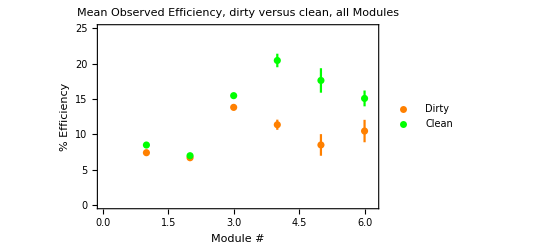

```mathematica
bigplot[mldfinal,mlcfinal]
```

```mathematica
(*Attempt to customize x-axis ticks*)Ticks-> {{"CIGS","CdTe","PolySi","ICBSi","HITSi","CIGSm"},Automatic}
```

Ticks→{{CIGS,CdTe,PolySi,ICBSi,HITSi,CIGSm},Automatic}

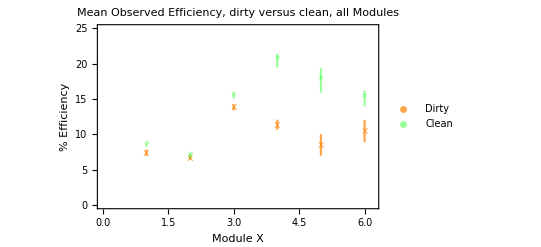

```mathematica
(*bigplot*)Show[
ErrorListPlot
[Table[{Mean[mldfinal[[All,i,15]]],StandardDeviation[mldfinal[[All,i,15]]]},{i,3,8}],
PlotMarkers->{"x"},
PlotRange-> {{0,6.2},{0,25}},
PlotLegends->{"Dirty"},
PlotStyle->Directive[Medium, Orange,PointSize->.02,Opacity@0.7]],
ErrorListPlot[Table[{Mean[mlcfinal[[All,i,15]]],StandardDeviation[mlcfinal[[All,i,15]]]},{i,3,8}],
PlotMarkers->{"*"},
PlotStyle->Directive[Medium,Green, PointSize->.03,Opacity@0.4], 
PlotLegends->{"Clean"}],
PlotLabel->"Mean Observed Efficiency, dirty versus clean, all Modules",
LabelStyle->{GrayLevel[0]}, BaseStyle->{FontWeight->"Bold",Font->"Helvetica",FontSize->10},Frame->{True,True,False,False},FrameLabel->{"Module X","% Efficiency"}
]
```

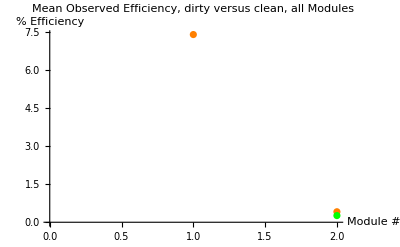

```mathematica
(*bigplotgen*)Show[
ErrorListPlot[{Mean[mldfinal[[All,3,15]]],StandardDeviation[mldfinal[[All,3,15]]]},PlotStyle->Orange],ErrorListPlot[{Mean[mlcfinal[[All,3,15]]],StandardDeviation[mlcfinal[[All,3,15]]]},PlotStyle->Green],AxesLabel->{HoldForm[ "Module #"],HoldForm["% Efficiency"]},PlotLabel->"Mean Observed Efficiency, dirty versus clean, all Modules",LabelStyle->{GrayLevel[0]},PlotLegends->{"Dirty","Clean"}
]
```

```mathematica
errorlistplotgen[filed1_,filed2_,filed3_,filed4_,filed5_,filed6_,filec1_,filec2_,filec3_,filec4_,filec5_,filec6_]:=ErrorListPlot[{
{{Mean[filed1],StandardDeviation[filed1]},{Mean[filed2],StandardDeviation[filed2]},{Mean[filed3],StandardDeviation[filed3]},{Mean[filed4],StandardDeviation[filed4]},{Mean[filed5],StandardDeviation[filed5]},{Mean[filed6],StandardDeviation[filed6]}},
{{Mean[filec1],StandardDeviation[filec1]},{Mean[filec2],StandardDeviation[filec2]},{Mean[filec3],StandardDeviation[filec3]},{Mean[filec4],StandardDeviation[filec4]},{Mean[filec5],StandardDeviation[filec5]},{Mean[filec6],StandardDeviation[filec6]}}
},
PlotLabel->"Mean of Bins for all Modules",AxesLabel->{HoldForm["Solar Module #" ],HoldForm["% Efficiency"]}]
```

### E.4 Compare this overall mldfinal/mlcfinal with if I had made one mega bin from the start. Sample size: {61,28} This is somewhat more selective than just plotting mldfinal/mlcfinal

```mathematica
megad=DeleteCases[Flatten[grabber[mldfinal,1.76,1.96,10.25,12.25,60,70],1],Null,3]; (*+-.2, +-2,+-10*)
megac=DeleteCases[Flatten[grabber[mlcfinal,1.76,1.96,10.25,12.25,60,70],1],Null,3];
Length[megad];
Length[megac];
```

OptionValue::nodef: Unknown option PlotLegends for Graphics.

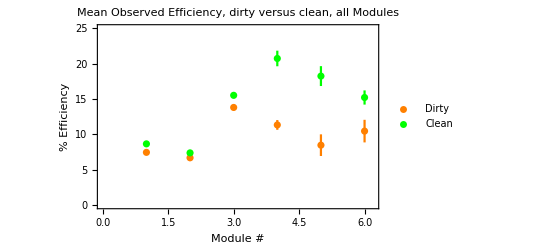

```mathematica
bigplot[megad,megac]
```

A superposition of the master list with all data from four days, or a more selective list, megad/c.

OptionValue::nodef: Unknown option PlotLegends for Graphics.

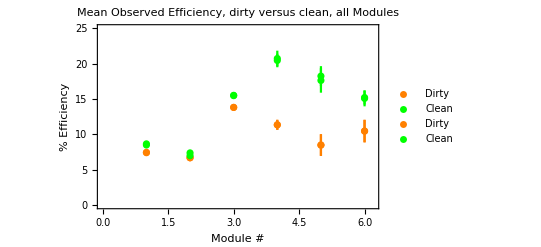

```mathematica
Show[bigplot[megad,megac],bigplot[mldfinal,mlcfinal]]
```

Standard deviation between efficiency values from all four days or from the more selective lists, mega(d)/(c)

```mathematica
StDev[file1_,file2_,module_]:=StandardDeviation[{Mean[file1[[All,module,15]]],Mean[file2[[All,module,15]]]}]
```

Module 1

```mathematica
StDev[megad,mldfinal,3]
StDev[megac,mlcfinal,3]
```

0.0347144

0.115972

Module2

```mathematica
StDev[megad,mldfinal,4]
StDev[megac,mlcfinal,4]
```

0.00638404

0.283819

Module3

```mathematica
StDev[megad,mldfinal,5]
StDev[megac,mlcfinal,5]
```

0.0103966

0.0336857

Module 4

```mathematica
StDev[megad,mldfinal,6]
StDev[megac,mlcfinal,6]
```

0.019255

0.200631

Module 5

```mathematica
StDev[megad,mldfinal,7]
StDev[megac,mlcfinal,7]
```

0.0224839

0.436529

Module 6

```mathematica
StDev[megad,mldfinal,8]
StDev[megac,mlcfinal,8]
```

0.00600489

0.092533

### ?? Weighted Average of efficiency from all the Bins; weighted by number of data points per efficiency value. 3 different weighted averages for APE, Int., and T; or at least for Int and T if APE’s 2 bins aren’t enough to do a weighted ave.

## F. Examine relationship between soiling density and change in dirty/clean efficiency

Differences in efficiency for each module between clean-dirty (in % efficiency)

```mathematica
dirtdensity={
{"1CIGSflex",0.2125},
{"2CdTe",0.9375},
{"3PolySi",1.5857},
{"4IBCSi",7.0275},
{"5HITSi",6.6175},
{"6CIGSmirror",3.9300}};
```

```mathematica
(*A list of dirt density measured from sampling soil off each panel*)density={{1,0.2125},{2,0.9375},{3,1.5857},{4,7.0275},{5,6.6175},{6,3.9300}};
```

```mathematica
(*A list difference in efficiency in the master clean and dirty lists*)effdiff={{1,Mean[mlcfinal[[All,3,15]]]-Mean[mldfinal[[All,3,15]]]},
{2,Mean[mlcfinal[[All,4,15]]]-Mean[mldfinal[[All,4,15]]]},
{3,Mean[mlcfinal[[All,5,15]]]-Mean[mldfinal[[All,5,15]]]},
{4,Mean[mlcfinal[[All,6,15]]]-Mean[mldfinal[[All,6,15]]]},
{5,Mean[mlcfinal[[All,7,15]]]-Mean[mldfinal[[All,7,15]]]},
{6,Mean[mlcfinal[[All,8,15]]]-Mean[mldfinal[[All,8,15]]]}}
```

{{1,1.08573},{2,0.287002},{3,1.6523},{4,9.07816},{5,9.11105},{6,4.60843}}

```mathematica
(*A list relative change in efficiency from dirty to clean*)effrel={{1,100*(Mean[mlcfinal[[All,3,15]]]-Mean[mldfinal[[All,3,15]]])/Mean[mlcfinal[[All,3,15]]]},
{2,100*(Mean[mlcfinal[[All,4,15]]]-Mean[mldfinal[[All,4,15]]])/Mean[mlcfinal[[All,4,15]]]},
{3,100*(Mean[mlcfinal[[All,5,15]]]-Mean[mldfinal[[All,5,15]]])/Mean[mlcfinal[[All,5,15]]]},
{4,100*(Mean[mlcfinal[[All,6,15]]]-Mean[mldfinal[[All,6,15]]])/Mean[mlcfinal[[All,6,15]]]},
{5,100*(Mean[mlcfinal[[All,7,15]]]-Mean[mldfinal[[All,7,15]]])/Mean[mlcfinal[[All,7,15]]]},
{6,100*(Mean[mlcfinal[[All,8,15]]]-Mean[mldfinal[[All,8,15]]])/Mean[mlcfinal[[All,8,15]]]}}
```

{{1,12.7746},{2,4.10616},{3,10.6777},{4,44.4041},{5,51.7034},{6,30.5544}}

This plot below visually shows the closeness in change in dirt density and change in efficiency on the panels from cleaning.

```mathematica
(*Altered from original form of "Plot" only*)TwoAxisPlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListPlot[#,FrameLabel->{"Module #","Dirt Density (g/m2)",None,"Change in Efficiency (%)"},Axes->True,PlotRange->{{0.8,6.2},Automatic},PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True, FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}, BaseStyle->{FontWeight->"Bold",Font->"Helvetica",FontSize->10}]]
```

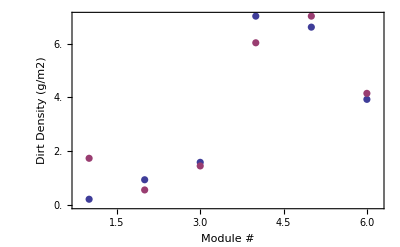

```mathematica
TwoAxisPlot[{dirtdensity[[All,2]],effrel}]
```

So what do the numbers say about dirt density and change in efficiency correlating?

```mathematica
(*correlation coefficient*) CorrelationTest[density,effrel]
```

0.957825

Below provides a line of fit for the correlation of the efficiency plotted by dirt density. The function generates a line function in terms of x using the data from the lists of effdiff and density defined above.

```mathematica
(*linear fit for density versus relative efficiency change clean-dirty*)Fit[Table[{density[[i,2]],effrel[[i,2]]},{i,1,Length[density]}],{1,x},x]
```

4.15144+6.36668 x

```mathematica
(*then define a plot line for this fitline*) c=Plot[{4.15144+6.36668x},{x,0,9},Axes->{False,False,False,False},PlotStyle->Directive[Medium, PointSize->.02,Opacity@0.5]];
```

Is this right?

```mathematica
xer=Sqrt[(1/4)*(1/4)*.001+(0.001/16)*(0.001/16)*4]
```

0.00790668

```mathematica
xerror=Sqrt[0.001*0.001+4*.2/2]
```

0.632456

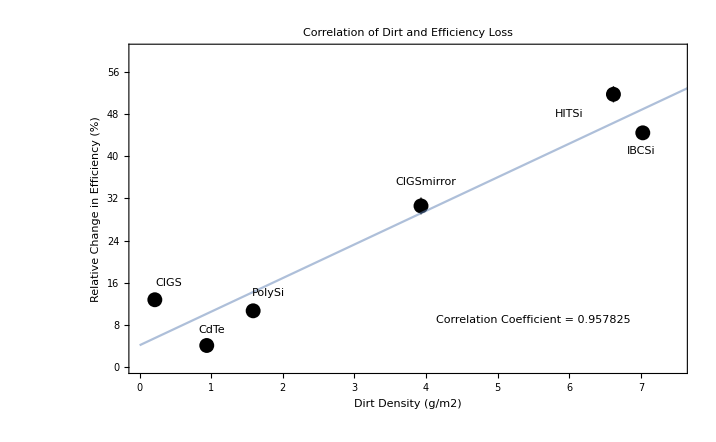

```mathematica
Show[ErrorListPlot[{
{{density[[1,2]],effrel[[1,2]]},ErrorBar[xer,StandardDeviation[mldfinal[[All,3,15]]]]},{{density[[2,2]],effrel[[2,2]]},ErrorBar[xer,StandardDeviation[mldfinal[[All,4,15]]]]},
{{density[[3,2]],effrel[[3,2]]},ErrorBar[xer,StandardDeviation[mldfinal[[All,5,15]]]]},
{{density[[4,2]],effrel[[4,2]]},ErrorBar[xer,StandardDeviation[mldfinal[[All,6,15]]]]},{{density[[5,2]],effrel[[5,2]]},ErrorBar[xer,StandardDeviation[mldfinal[[All,7,15]]]]},{{density[[6,2]],effrel[[6,2]]},ErrorBar[xer,StandardDeviation[mldfinal[[All,8,15]]]]}
} ,PlotStyle->Directive[Thin,Black,PointSize->.015],
PlotRange->{{0,7.5},{0,60}},
Epilog->{Text["Correlation Coefficient = 0.957825",{5.5,9}],Text["CIGS",{0.4,16}],
Text["CdTe",{1,7}],Text["PolySi",{1.8,14}],Text["CIGSmirror",{4,35}],Text["HITSi",{6,48}],Text["IBCSi",{7,41}]},
 BaseStyle->{FontWeight->"Bold",Font->"Helvetica",FontSize->10}],c,LabelStyle->Black,Frame->{True,True,False,False},
FrameLabel->{"Dirt Density (g/m2)","Relative Change in Efficiency (%)",Below},PlotLabel->"Correlation of Dirt and Efficiency Loss",Font->"Helvetica"]
```

### Export Figures

Export figures into desired directory. You need to use quotes for directory and file names, and put \\ before the desired name.

Example: Export[SetDirectory[“P:\\Engineering\\SolarField\\Talia\\”]<>”\\new2.jpg”,Magnify[correlationplot,2],Background→White]

```mathematica
export[dir_,name_,figure_]:=Export[SetDirectory[dir]<>name,Magnify[figure,2],Background->White];
```